# Disk

### Author

Eric W. Weisstein
June 12, 2015

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Laminae/Disk.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Disk.html.

©2015 Wolfram Research, Inc. except for portions noted otherwise

### Definitions

```mathematica
ineq=x^2+y^2<=a^2;
```

```mathematica
reg=Disk[{0,0},a];
```

```mathematica
implreg=ImplicitRegion[x^2+y^2≤a^2,{x,y}];
```

```mathematica
assum=a>0;
```

```mathematica
area=π a^2;
```

```mathematica
ent="Disk";
```

## Plots

### Entity Diagram

```mathematica
LaminaData[ent,"Diagram"]
```

-Graphics-

### Entity ImplicitRegion

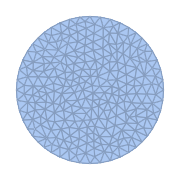

```mathematica
Show[DiscretizeRegion@LaminaData[ent,"ImplicitRegion"][1],ImageSize->Small]
```

### Entity ParametricRegion

DiscretizeRegion::drc: Available methods not able to resolve all components of dimension less than the embedding dimension 2; these may be omitted from the result.

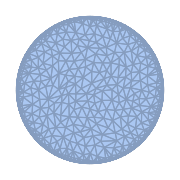

```mathematica
Show[DiscretizeRegion@LaminaData[ent,"ParametricRegion"][1],ImageSize->Small]
```

bug(295139)

### Entity Region

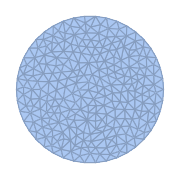

```mathematica
Show[DiscretizeRegion@LaminaData[ent,"Region"][1],ImageSize->Small]
```

### DiscretizeRegion

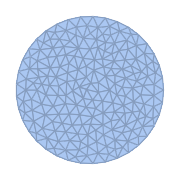

```mathematica
Block[{a=1},Show[DiscretizeRegion[reg],ImageSize->Small]]
```

### RegionPlot

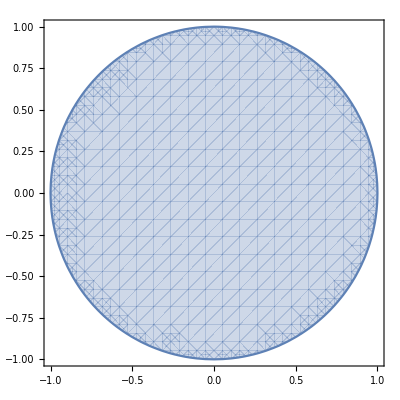

```mathematica
RegionPlot[x^2+y^2≤1,{x,-1,1},{y,-1,1}]
```

### SemialgebraicRegionPlot

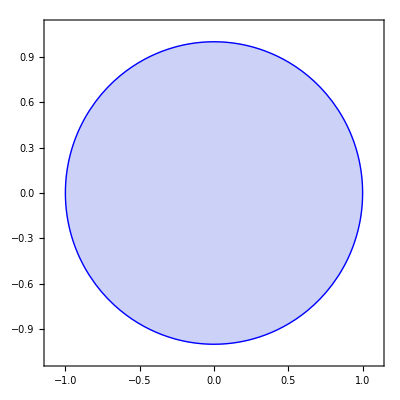

```mathematica
Region`SemialgebraicRegionPlot[ImplicitRegion[x^2+y^2≤1,{x,y}],{{-1.1,1.1},{-1.1,1.1}}]
```

## Regions

```mathematica
LaminaData[ent,"ImplicitRegion"]
```

Function[{a},ImplicitRegion[x^2+y^2≤a^2,{x,y}]]

```mathematica
LaminaData[ent,"ParametricRegion"]
```

Function[a,ParametricRegion[{r Cos[q],r Sin[q]},{{q,0,2 π},{r,0,a}}]]

```mathematica
LaminaData[ent,"Region"]
```

Function[a,Disk[{0,0},a]]

## Properties

### Area

#### Entity

```mathematica
EntityValue[Entity[ent, ent], "Area"][a]
```

a^2 π

#### Integrate

```mathematica
Assuming[a>0,FullSimplify[Area[ineq[x,y],{x,y}]]]
```

a^2 π

#### Area

```mathematica
Area[reg]
```

a^2 π

```mathematica
Assuming[assum,Area[implreg]]
```

a^2 π

```mathematica
Assuming[assum,Area[EntityValue[Entity[ent,ent],"ImplicitRegion"][a]]]
```

a^2 π

```mathematica
Assuming[assum,Area[EntityValue[Entity[ent,ent],"ParametricRegion"][a]]]
```

a^2 π

```mathematica
Assuming[assum,Area[EntityValue[Entity[ent,ent],"Region"][a]]]
```

a^2 π

#### RegionMeasure

```mathematica
Assuming[a>1,RegionMeasure[ImplicitRegion[x^2+y^2≤a^2,{x,y}]]]//Timing
```

{1.08677,a^2 π}

```mathematica
Assuming[a>1,RegionMeasure[ImplicitRegion[x^2+y^2≤a^2,{x,y}],2]]//Timing
```

{1.15178,a^2 π}

```mathematica
Assuming[assum,RegionMeasure[reg]]
```

a^2 π

### Boundary

```mathematica
LaminaData[ent,"BoundaryCurve"]
```

circle

```mathematica
LaminaData[ent,"Boundary"]
```

Function[{a},RegionBoundary[Disk[{0,0},a]]]

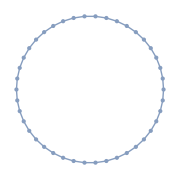

```mathematica
Show[DiscretizeRegion[LaminaData[ent,"Boundary"][1]],ImageSize->Small]
```

```mathematica
LaminaData[ent,"BoundaryMeshRegion"]
```

Missing[NotAvailable]

```mathematica
LaminaData[ent,"MeshRegion"]
```

Missing[NotAvailable]

### AreaInertiaTensor

```mathematica
Assuming[a>0,FullSimplify[AreaInertiaTensor[ineq[x,y],{x,y}]]]
```

{{(a^4 π)/4,0},{0,(a^4 π)/4}}

### Centroid

#### Package

```mathematica
Assuming[a>0,FullSimplify[Centroid[ineq[x,y],{x,y}]]]
```

{0,0}

#### RegionCentroid

```mathematica
RegionCentroid[R]//Timing
```

RegionCentroid::nmet: Unable to compute the centroid of region ImplicitRegion[x^2 + y^2 ≤ a^2, {x, y}].

{0.24829,RegionCentroid[ImplicitRegion[x^2+y^2≤a^2,{x,y}]]}

```mathematica
RegionCentroid[R,2]//Timing
```

RegionCentroid::nonopt: Options expected (instead of 2) beyond position 1 in RegionCentroid[ImplicitRegion[x^2 + y^2 ≤ a^2, {x, y}], 2]. An option must be a rule or a list of rules.

{0.16037,RegionCentroid[ImplicitRegion[x^2+y^2≤a^2,{x,y}],2]}

```mathematica
RegionMeasure[R]
```

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[x^2 + y^2 ≤ a^2, {x, y}].

RegionMeasure[ImplicitRegion[x^2+y^2≤a^2,{x,y}]]

-------- Original Message --------
Subject: Re: RegionMeasure[x^2 + y^2 <= a^2]
Date: Thu, 24 Oct 2013 17:10:17 -0500
From: Adam Strzebonski <adams@wolfram.com>
To: Eric Weisstein <eww@wolfram.com>

The definition of RegionCentroid requires that the dimensions
of the measure and of the region agree, so it cannot take
a dimension argument. RegionCentroid will work for regions that
depend on symbolic parameters when we have code for computing
integrals over such regions. Currently RegionMeasure[R, n] defaults
to Integral[Boole[implicit description of R], vars] when n is equal
to the embedding dimension, and fails for other n.

Adam

### Convex

```mathematica
Region`ConvexRegionQ[reg]//Timing
```

{0.009998,True}

```mathematica
Region`ConvexRegionQ[implreg]//Timing
```

{2.82957,True}

### GeneralizedDiameter

```mathematica
ineqs=And@@ineq@@@{{x1,y1},{x2,y2}}/.a->1
```

x1^2+y1^2≤1&&x2^2+y2^2≤1

```mathematica
Maximize[{(x1-x2)^2+(y1-y2)^2,ineqs},{x1,x2,y1,y2}]//Timing
```

{0.319951,{4,{x1→-7/8,x2→7/8,y1→-(√15)/8,y2→(√15)/8}}}

### RadiiOfGyration

```mathematica
Assuming[a>0,FullSimplify[RadiiOfGyration[ineq[x,y],{x,y}]]]
```

{a/2,a/2}

### Regions

```mathematica
EntityValue[Entity[ent,ent],"ImplicitRegion"][a]
```

ImplicitRegion[x^2+y^2≤a^2,{x,y}]

```mathematica
EntityValue[Entity[ent,ent],"ParametricRegion"][a]
```

ParametricRegion[{{Cos[q] r,r Sin[q]},0≤q≤2 π&&0≤r≤a},{q,r}]

```mathematica
EntityValue[Entity[ent,ent],"Region"][a]
```

Disk[{0,0},a]